13.4625

Import::nffil: File not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

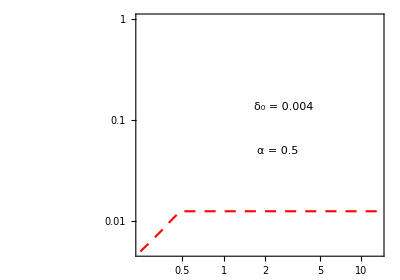
-Graphics-τ (fm/c)

```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];

t0=0.25;
dt0=0.005;

dtAdapt =Import[wd<>"/output/dt_adaptive.dat"];
tf=dtAdapt[[-1,1]]
dtAdapt=Join[{{t0,dt0}},dtAdapt];
dtAdapt=Interpolation[dtAdapt];

dtCFL = Import[wd<>"/output/dt_CFL.dat"];
dtCFL=Interpolation[dtCFL];

delta0=Panel[Grid[{{Style["δ_0 = 0.004",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
alpha=Panel[Grid[{{Style["α = 0.5",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
dt=Panel[Grid[{{Style["Δτ_n",FontSize->18,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
CFL=Panel[Grid[{{Style["Δτ_CFL",FontSize->18,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];

min = {0.009,0};
maj={0.016,0};

logticks = {{0.0001,"10^-4",maj},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"10^-3",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"0.01",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},
{0.1,"0.1",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},
{1,"1",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},
{10,"10",maj},{20,"",min},{30,"",min},{40,"",min},{50,"",min},{60,"",min},{70,"",min},{80,"",min},{90,"",min},
{100,"100",maj},{200,"",min},{300,"",min},{400,"",min},{500,"",min},{600,"",min},{700,"",min},{800,"",min},{900,"",min},
{1000,"10^3",maj},{2000,"",min},{3000,"",min},{4000,"",min},{5000,"",min},{6000,"",min},{7000,"",min},{8000,"",min},{9000,"",min},{10000,"10^4",maj},{20000,"",min}};

nologticks =  {{0.0001,"",maj},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},
{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},
{1,"",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},
{10,"",maj},{20,"",min},{30,"",min},{40,"",min},{50,"",min},{60,"",min},{70,"",min},{80,"",min},{90,"",min},
{100,"",maj},{200,"",min},{300,"",min},{400,"",min},{500,"",min},{600,"",min},{700,"",min},{800,"",min},{900,"",min},
{1000,"",maj},{2000,"",min},{3000,"",min},{4000,"",min},{5000,"",min},{6000,"",min},{7000,"",min},{8000,"",min},{9000,"",min},{10000,"",maj},{20000,"",min}};

timeticks = {{0.01,"0.01",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"0.1",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"1.0",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"10",maj},{20,"",min}};

notimeticks = {{0.01,"",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"",maj},{20,"",min}};

redTran={Red,AbsoluteThickness[1.5],Opacity[0.3]};
red={Red,AbsoluteDashing[{8,6.5}],AbsoluteThickness[1.5]};

timestep=LogLogPlot[{dtCFL[t],dtAdapt[t]},{t,t0,tf},PlotRange->{{t0,tf},{dt0,1}},Frame->True,FrameTicks->{{logticks,nologticks},{timeticks,notimeticks}},PlotStyle->{redTran,red},FrameStyle->Black,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->400,Epilog->{Inset[dt,{-3,-4.75}],Inset[CFL,{-2.,-1.5}],Inset[delta0,{1,-2.}],Inset[alpha,{0.91,-3.}]}];

timeplot=Panel[GraphicsGrid[{{timestep}},Spacings->{0,0}],{Style["τ (fm/c)",FontFamily->"Arial",FontSize->16]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]

Export[wd<>"/timestep.pdf",%];
```